```mathematica
SetDirectory[NotebookDirectory[]];
Off[NDSolve::"ndsz",NDSolve::maxit,NDSolve::"noout"]
$PlotTheme=None;(* plots in Mathematica10 looks like in previous versions *)
```

Charged particle trajectory in magnetic field around black hole is calculated using Hamiltonian formalism -  more information can be found in: 
M.Kološ, Z.Stuchlík, A.Tursunov: “Quasi-harmonic oscillatory motion of charged particles around a Schw. black hole immersed in a uniform mag. field”, Classical and Quantum Gravity 32 (16), 165009
A.Tursunov, Z.Stuchlík, M.Kološ: “Circular orbits and related quasiharmonic oscillatory motion of charged particles around weakly mag. rotating black holes”, Physical Review D 93 (8), 084012 (2016)
Z.Stuchlík, M.Kološ “Acceleration of the charged particles due to chaotic scattering in the combined black hole grav. field and asymptotically uniform mag. field”, The European Physical Journal C (2006)

This file works for Kerr metrics  g_αβ and electromagnetic field A_α=(A_t,0, 0, A_ϕ)

## GiveMeTrajectory

```mathematica
Clear["Global`*"];M=1;

(*---- Metrics coefficients for Kerr BH ----*)
(*velka sigma*) R2[r_,θ_]:=r^2+a^2 Cos[θ]^2;(*trojuhelnicek*) TR[r_,θ_]:=r^2-2M r +a^2;

(* lower indexies *) gtt[r_,θ_]:=-(1-(2M r)/R2[r,θ]);gtϕ[r_,θ_]:=-(2 r M a Sin[θ]^2)/R2[r,θ];
gϕϕ[r_,θ_]:=(r^2+a^2+(2  M r a^2)/R2[r,θ] Sin[θ]^2)Sin[θ]^2;grr[r_,θ_]:=R2[r,θ]/TR[r,θ];gθθ[r_,θ_]:= R2[r,θ];

(*metrika s hornimi indexy*) gUtt[r_,θ_]:=-1/TR[r,θ](r^2+a^2+(2  M r a^2)/R2[r,θ] Sin[θ]^2);gUtϕ[r_,θ_]:=-(2 M a r)/(TR[r,θ] R2[r,θ]);

gUϕϕ[r_,θ_]:=(TR[r,θ]- a^2 Sin[θ]^2)/(TR[r,θ]R2[r,θ] Sin[θ]^2);gUrr[r_,θ_]:=TR[r,θ]/R2[r,θ];gUθθ[r_,θ_]:=1/R2[r,θ];
(*---- Metrics coefficients for Kerr BH ----*)

(*---- electromagnetic 4 potential for uniform magnetic field B (BH with Wald charge Q=2aB) ----*)
(* B=ℬ; ℬ = (q Bstrengt)/(2 m) *)
qAt[r_,θ_]:=B gtϕ[r,θ];
qAϕ[r_,θ_]:=B gϕϕ[r,θ];
(*---- electromagnetic 4 potential for uniform magnetic field B (BH with Wald charge Q=2aB) ----*)

(*---- effective potential for charged paricle motion ----*)
amA[r_,θ_,LL_]:=-gUtt[r,θ];
amB[r_,θ_,LL_]:=2(gUtϕ[r,θ](LL-qAϕ[r,θ])-gUtt[r,θ]qAt[r,θ]);
amC[r_,θ_,LL_]:=-gUϕϕ[r,θ](LL-qAϕ[r,θ])^2-gUtt[r,θ] qAt[r,θ]^2+2gUtϕ[r,θ]qAt[r,θ](LL-qAϕ[r,θ])-1;
Veff[r_,θ_,LL_]:=(-amB[r,θ,LL]+√(amB[r,θ,LL]^2-4amA[r,θ,LL]amC[r,θ,LL]))/(2amA[r,θ,LL]);
(*---- effective potential for charged paricle motion ----*)

(* specific energy and angular momentum for circular orbit in Kerr *)
kerrEE[r_,a_]:=(1-2/r+a/r^(3/2))/(√(1-3/r+2a/r^(3/2)));kerrLL[r_,a_]:=(r^(1/2)-2a/r+a^2/r^(3/2))/(√(1-3/r+2a/r^(3/2)));
(* ISCO position in Kerr *)
Z1[a_]:=1+(1-a^2)^(1/3)((1+a)^(1/3)+(1-a)^(1/3));Z2[a_]:=√(3 a^2+Z1[a]^2);
rmsM[a_]:=3+Z2[a]-√((3-Z1[a])(3+Z1[a]+2Z2[a]));rmsP[a_]:=3+Z2[a]+√((3-Z1[a])(3+Z1[a]+2Z2[a]));
rmbM[a_]:=2-a+2 √(1-a);rmbP[a_]:=2+a+2 √(1+a);
pphM[a_]:=2(1+Cos[2/3 ArcCos[-a]]);pphP[a_]:=2(1+Cos[2/3 ArcCos[+a]]);
rhP[a_]:=1+√(1-a^2);(* Kerr BH outer horizon *)

(* 2D - polar coordinates *)
XX[r_,ϕ_]:=r Cos[ϕ];YY[r_,ϕ_]:=r Sin[ϕ];

(* 3D - spherical coordinates *)
XXX[r_,θ_,ϕ_]:=r Sin[θ] Cos[ϕ];
YYY[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ];
ZZZ[r_,θ_,ϕ_]:=r Cos[θ];

(* this function will calculate charged particle trajectory *)
GiveMeTrajectory[r0_,θ0_,LL_,xEND_]:=(
Clear[r,pr,θ, pθ,ϕ];
EE=Veff[r0,θ0,LL];(* EE=Veff[r0,θ0,LL] - four velocity norming condition: p^μ Subscript[p, ν]=-m^2 <=> H=0 *)

(*---- Hamiltonian a equations of motion ----*)
(* H = 1/2 g^μν(Subscript[π, μ]-Subscript[qA, μ])(Subscript[π, ν]-Subscript[qA, ν])+1/2; where g^rr=gUrr; Subscript[π, r]=Pir; Subscript[qA, r]=qAr; x^r=r; Subscript[p, r]=pr... *)
(* if symmetries (E,L constant of motion) will be aplied Hamiltonian can be reduced: *)
HoHo[r_,θ_,pr_,pθ_]:=1/2 gUrr[r,θ] pr^2+1/2 gUθθ[r,θ] pθ^2+1/2+1/2( gUtt[r,θ](-EE-qAt[r,θ])^2+2gUtϕ[r,θ](-EE-qAt[r,θ])(LL-qAϕ[r,θ])+gUϕϕ[r,θ](LL-qAϕ[r,θ])^2);
(* pr = Subscript[p, r], qAt = Subscript[qA, t] - lower index *) (* r = x^r, gUrr = g^rr - upper index *)
DrHoHo[r_,θ_,pr_,pθ_]:=D[HoHo[r,θ,pr,pθ], r];DθHoHo[r_,θ_,pr_,pθ_]:=D[HoHo[r,θ,pr,pθ], θ];HamI=HoHo[r[τ],θ[τ],pr[τ],pθ[τ]];

Equations ={
r'[τ]   ==    gUrr[r[τ] ,θ[τ]]pr[τ],pr'[τ]  == -DrHoHo[r[τ],θ[τ],pr[τ],pθ[τ]],
θ'[τ]   ==   gUθθ[r[τ] ,θ[τ] ]pθ[τ],pθ'[τ]  ==-DθHoHo[r[τ],θ[τ],pr[τ],pθ[τ]],
ϕ'[τ]   ==   -gUtϕ[r[τ] ,θ[τ]]EE+ gUϕϕ[r[τ] ,θ[τ]]LL-gUtϕ[r[τ] ,θ[τ]]qAt[r[τ],θ[τ]]-gUϕϕ[r[τ] ,θ[τ]]qAϕ[r[τ],θ[τ]]  
(* ϕ' = p^ϕ = g^ϕt Subscript[p, t] + g^ϕϕ Subscript[p, ϕ] = -g^ϕtE - g^ϕt Subscript[qA, t] + g^ϕϕ L - g^ϕϕ Subscript[qA, ϕ] *) 
(* t' = we do not need to calculate, becouse the model is nedependent of t and ϕ (stacionarity, axill symmetry) and t coordinate is not used for plots (as ϕ does) *)
};
IntCond ={r[0]==r0, pr[0]==0,θ[0]==θ0, pθ[0]==0,ϕ[0]==0};

(*---- Hamiltonian a equations of motion ----*)

(*---- trajectory calculation ----*)
stepsize=10^-4;
Switch[NumMethod,
1,Metoda={"StiffnessSwitching", Method->{ {"Projection", Method->{"ExplicitRungeKutta","DifferenceOrder"->9},"Invariants"->HamI},Automatic}};,
2,stepsize=10^-4;Metoda={"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->4}};,
_,Metoda=Automatic
];(* put your favourite numerical method here *)

draha=NDSolve[{Equations,IntCond},{r,pr,θ,pθ,ϕ},{τ,0,xEND},{Method->{"EventLocator","Event"->{r[τ]-xRH,r[τ]-xInfinity},"EventAction":>{Throw[ Null,"StopIntegration"],Throw[Null, "StopIntegration"]},"Method"->Metoda},{StartingStepSize->stepsize,MaxSteps->∞}}];
ipub=r/.draha[[1,1]];domain=ipub["Domain"];{begin,end} = domain[[1]];
(*---- trajectory calculation ----*)

);


ShowTrajectory[colour_]:=(
(* this function will show particle trajectory
colour = particle trajectory colour; 
*)
ϕ0=0;
GraphicsGrid[{{pic1=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{colour},Frame->True,BaseStyle->fontyW,PlotRange->oblast2D,Prolog->{LightGray,Disk[{0,0},RH]},
Epilog->{PointSize[0.02],Point[{XXX[r0,θ0,ϕ0],YYY[r0,θ0,ϕ0]}]},FrameLabel->{"x","y"},RotateLabel->False,Axes->False,ImageSize->ImSz],
pic2=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]],ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{colour},Frame->True,BaseStyle->fontyW,PlotRange->oblast2D,Prolog->{LightGray,Disk[{0,0},RH]},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,
Epilog->{PointSize[0.02],Point[{XXX[r0,θ0,ϕ0],ZZZ[r0,θ0,ϕ0]}],Text[Row[{"r_0≐",Round[r0,0.01],"| θ_0≐",Round[θ0,0.01]}],Scaled[{0.5,0.1}]],Text[Row[{"E≐",Round[EE,0.01]," | L≐",Round[LL,0.01]}],Scaled[{0.5,0.9}]]
}],
pic3=Show[
ContourPlot[Veff[√(xx^2+zz^2),ArcTan[xx/zz],LL]==EE,{xx,0,oblast1D[[2]]},{zz,oblast1D[[1]]/2,oblast1D[[2]]/2},ContourStyle->{{Red,Thick,Dotted}},Frame->True,BaseStyle->fontyW,FrameLabel->{"x","z"},AspectRatio->1,Frame->True,RotateLabel->False,Axes->False,ImageSize->ImSz,Epilog->{LightGray,Disk[{0,0},RH],Black,PointSize[0.02],Point[{XXX[r0,θ0,ϕ0],ZZZ[r0,θ0,ϕ0]}]}],
ParametricPlot[{XXX[r[τ],θ[τ],0],ZZZ[r[τ],θ[τ],0] }/.draha,{τ,begin,end},PlotStyle->{colour}]
],
pic4=Show[ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotRange->oblast3D,BoxStyle->{Black},PlotStyle->{colour},ViewPoint->{0,-3,1},Ticks->None,ImageSize->ImSz],
Graphics3D[{{Black,Text[Style[param,fontyW],{0,0.5oblast1D[[1]],1oblast1D[[1]]}]},{LightGray,Sphere[{0,0,0},RH]},{Black,PointSize[0.02],Point[{XXX[r0,θ0,ϕ0],YYY[r0,θ0,ϕ0],ZZZ[r0,θ0,ϕ0]}]}}],Lighting->"Neutral"]
}},Spacings->0,ImageSize->1000]
);

fonty=15;fontyW={FontSize->15,Background->White};ImSz=250;
oblast1D={-10.5,10.5};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};

RH=rhP[a];xRH=RH+10^-2;xInfinity=1000;NumMethod=1;
```

## some trajectories in uniform magnetic field

```mathematica
a=0.9;B=-0.1;konec=200;param=Row[{"a=",a," | ℬ =",B}];(* initial position and ang.mom. L *) r0=5;θ0=1.1;LL=3.5;
GiveMeTrajectory[r0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
a=0.9;B=0.1;konec=200;param=Row[{"a=",a," | ℬ =",B}];(* initial position and ang.mom. L *) r0=5;θ0=1.1;LL=3.5;
GiveMeTrajectory[r0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

```mathematica
a=0.9;B=1;konec=200;param=Row[{"a=",a," | ℬ =",B}];(* initial position and ang.mom. L *) r0=6;θ0=1.5;LL=2.5;
GiveMeTrajectory[r0,θ0,LL,konec];ShowTrajectory[Blue]
```

-Graphics-

## effective potential

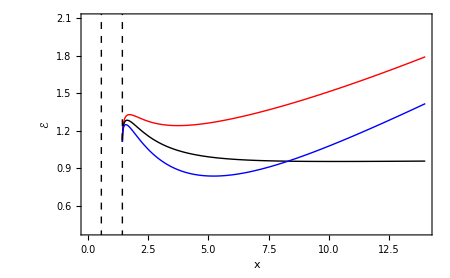

```mathematica
a=0.9;LL=3.5;RH1=1-√(1-a^2);RH2=1+√(1-a^2);
Plot[{
B=-0.1;Veff[x,Pi/2,LL],B=0;Veff[x,Pi/2,LL],B=0.1;Veff[x,Pi/2,LL]
},{x,0,14},PlotPoints->40,PlotRange->{0.4,2.1},ImageSize->450,BaseStyle->15,Frame->True,RotateLabel->False,FrameLabel->{"x","ℰ"},PlotStyle->{Red,Black,Blue},Epilog->{Black,Dashed,Line[{{RH1,0},{RH1,10}}],Line[{{RH2,0},{RH2,10}}]}]
```

## neutral particle ionization and the motion of the charged product

Z.Stuchlík, M.Kološ “Acceleration of the charged particles due to chaotic scattering in the combined black hole gravitational field and asymptotically uniform magnetic field”, The European Physical Journal C (2006)

```mathematica
fceQ[r_,θ_,a_]:=√(r^2-a^2 Cos[θ]^2);
fceRO[r_,θ_,a_]:=√(r^2+a^2 Cos[θ]^2);
fceLLz[r_,θ_,a_,q_,ro_]:=(q/ro^2 √(1/r)(r^2+a^2)Sin[θ]-(2a r)/ro^2 Sin[θ]^2)/√(1-(3 r)/ro^2+(2a q)/ro^2 √(1/r)Sin[θ]+a^2/(ro^2 r)Cos[θ]^2);
fceEE[r_,θ_,a_,q_,ro_]:=(1-(2r)/ro^2+(a q)/ro^2 √(1/r)Sin[θ])/√(1-(3 r)/ro^2+(2a q)/ro^2 √(1/r)Sin[θ]+a^2/(ro^2 r)Cos[θ]^2);

fIONIZCE[]:=(
(* qAt[r_,θ_]:=B gtϕ[r,θ]; qAϕ[r_,θ_]:=B gϕϕ[r,θ];
B<0 (* - *) EEm=EE0-qAtQ;LLm=LL0+qAϕQ;
B>0 (* + *) EEp=EE0-qAtQ;LLp=LL0+qAϕQ; *)
(* (0) neutral particle on circular orbit with some inclination to equatorial palne *)
EE0=fceEE[r0,θ0,a,fceQ[r0,θ0,a],fceRO[r0,θ0,a]];LL0=fceLLz[r0,θ0,a,fceQ[r0,θ0,a],fceRO[r0,θ0,a]];
(* (m) ionized particle, minus case *) EEm=EE0+B gtϕ[r0,θ0]; LLm=LL0-B gϕϕ[r0,θ0];
(* (p) ionized particle, minus case *) EEp=EE0-B gtϕ[r0,θ0]; LLp=LL0+B gϕϕ[r0,θ0];

Row[{"E0=",EE0,", L0=",LL0," | Em=",EEm,", Lm=",LLm," | Ep=",EEp,", Lp=",LLp}]

);
```

E0=0.908635, L0=2.591 | Em=0.552338, Lm=-23.2792 | Ep=1.26493, Lp=28.4612

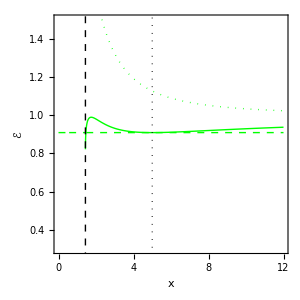
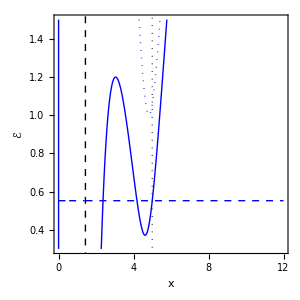
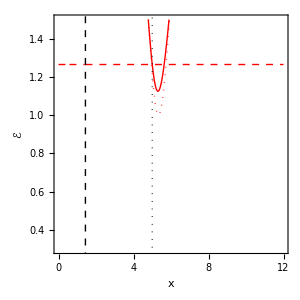

```mathematica
a=0.9;BB=1;(*BB=abs. value of B*) r0=5;θ0=Pi/2+0.1;B=BB;zz=10^7;fIONIZCE[]
figX[color_]:=Plot[{EE,Veff[x,θ0,LL],Veff[√(x^2+zz^2),ArcTan[x/zz],LL]},{x,0,12},PlotPoints->40,PlotRange->{0.3,1.5},BaseStyle->15,Frame->True,RotateLabel->False,FrameLabel->{"x","ℰ"},PlotStyle->{{color,Dashed},{color},{color,Dotted}},AspectRatio->1,ImageSize->300,Epilog->{Black,Dashed,Line[{{RH,0},{RH,10}}],Dotted,Line[{{r0,0},{r0,10}}]}];
{EE=EE0;LL=LL0;B=0;figX[Green],EE=EEm;LL=LLm;B=-BB;figX[Blue],EE=EEp;LL=LLp;B=BB;figX[Red]}
```

```mathematica
konec=100;
(*neutral*) B=0;param=Row[{"a=",a," | ℬ =",B}];LL=LL0;GiveMeTrajectory[r0,θ0,LL,konec];ShowTrajectory[Green]
(*ionized - *) B=-BB;param=Row[{"a=",a," | ℬ =",B}];LL=LLm;GiveMeTrajectory[r0,θ0,LL,konec];ShowTrajectory[Blue]
(*ionized + *) B=BB;param=Row[{"a=",a," | ℬ =",B}];LL=LLp;GiveMeTrajectory[r0,θ0,LL,konec];ShowTrajectory[Red]
```

-Graphics-

-Graphics-

-Graphics-